```mathematica
Clear["Global`*"]
```

```mathematica
datos=Flatten[Import["C:\\Users\\Fabi\\Desktop\\Carga y descarga.xlsx"],1];
```

```mathematica
datos//TableForm
```

Tiempo [s] | Carga [V] | ε - Vc (t) |  | Tiempo [s] | Descarga [V] |  |  |  |  |  |  |  |  |  |  | 
1.58 | 0.8 | 11.2 |  | 1.87 | 10.26 |  |  |  |  |  |  |  |  |  |  | 
1.99 | 1.08 | 10.92 |  | 2.37 | 10. |  |  |  |  |  |  |  |  |  |  | 
2.37 | 1.34 | 10.66 |  | 2.53 | 9.73 |  |  |  |  |  |  |  |  |  |  | 
2.81 | 1.6 | 10.4 |  | 2.98 | 9.48 |  |  |  |  |  |  |  |  |  |  | 
3.29 | 1.85 | 10.15 |  | 3.37 | 9.23 |  |  |  |  |  |  |  |  |  |  | 
3.48 | 2.09 | 9.91 |  | 3.81 | 8.99 |  |  |  |  |  |  |  |  |  |  | 
3.87 | 2.33 | 9.67 |  | 4.18 | 8.76 |  |  |  |  |  |  |  |  |  |  | 
4.37 | 2.56 | 9.44 |  | 4.58 | 8.53 |  |  |  |  |  |  |  |  |  |  | 
4.68 | 2.78 | 9.22 |  | 4.99 | 8.31 |  |  |  |  |  |  |  |  |  |  | 
5.18 | 3. | 9. |  | 5.49 | 8.1 |  |  |  |  |  |  |  |  |  |  | 
5.48 | 3.21 | 8.79 |  | 5.81 | 7.89 |  |  |  |  |  |  |  |  |  |  | 
5.87 | 3.41 | 8.59 |  | 6.21 | 7.68 |  |  |  |  |  |  |  |  |  |  | 
6.34 | 3.62 | 8.38 |  | 6.65 | 7.49 |  |  |  |  |  |  |  |  |  |  | 
6.68 | 3.81 | 8.19 |  | 6.92 | 7.3 |  |  |  |  |  |  |  |  |  |  | 
7.18 | 4. | 8. |  | 7.31 | 7.11 |  |  |  |  |  |  |  |  |  |  | 
7.48 | 4.19 | 7.81 |  | 7.71 | 6.92 |  |  |  |  |  |  |  |  |  |  | 
7.98 | 4.37 | 7.63 |  | 8.15 | 6.75 |  |  |  |  |  |  |  |  |  |  | 
8.27 | 4.54 | 7.46 |  | 8.49 | 6.57 |  |  |  |  |  |  |  |  |  |  | 
8.79 | 4.71 | 7.29 |  | 8.87 | 6.41 |  |  |  |  |  |  |  |  |  |  | 
9.08 | 4.88 | 7.12 |  | 9.31 | 6.24 |  |  |  |  |  |  |  |  |  |  | 
9.48 | 5.04 | 6.96 |  | 9.69 | 6.08 |  |  |  |  |  |  |  |  |  |  | 
9.87 | 5.2 | 6.8 |  | 10.19 | 5.93 |  |  |  |  |  |  |  |  |  |  | 
10.29 | 5.35 | 6.65 |  | 10.48 | 5.77 |  |  |  |  |  |  |  |  |  |  | 
10.64 | 5.5 | 6.5 |  | 10.81 | 5.63 |  |  |  |  |  |  |  |  |  |  | 
11.14 | 5.65 | 6.35 |  | 11.31 | 5.48 |  |  |  |  |  |  |  |  |  |  | 
11.58 | 5.79 | 6.21 |  | 11.69 | 5.34 |  |  |  |  |  |  |  |  |  |  | 
11.98 | 5.93 | 6.07 |  | 12.18 | 5.21 |  |  |  |  |  |  |  |  |  |  | 
12.37 | 6.06 | 5.94 |  | 12.48 | 5.07 |  |  |  |  |  |  |  |  |  |  | 
12.64 | 6.19 | 5.81 |  | 12.93 | 4.94 |  |  |  |  |  |  |  |  |  |  | 
13.18 | 6.32 | 5.68 |  | 13.31 | 4.82 |  |  |  |  |  |  |  |  |  |  | 
13.48 | 6.44 | 5.56 |  | 13.65 | 4.7 |  |  |  |  |  |  |  |  |  |  | 
13.87 | 6.56 | 5.44 |  | 14.08 | 4.58 |  |  |  |  |  |  |  |  |  |  | 
14.29 | 6.68 | 5.32 |  | 14.49 | 4.46 |  |  |  |  |  |  |  |  |  |  | 
14.64 | 6.79 | 5.21 |  | 14.81 | 4.35 |  |  |  |  |  |  |  |  |  |  | 
14.98 | 6.91 | 5.09 |  | 15.21 | 4.24 |  |  |  |  |  |  |  |  |  |  | 
15.48 | 7.02 | 4.98 |  | 15.58 | 4.13 |  |  |  |  |  |  |  |  |  |  | 
15.99 | 7.12 | 4.88 |  | 15.99 | 4.03 |  |  |  |  |  |  |  |  |  |  | 
16.31 | 7.22 | 4.78 |  | 16.37 | 3.92 |  |  |  |  |  |  |  |  |  |  | 
16.64 | 7.32 | 4.68 |  | 16.71 | 3.82 |  |  |  |  |  |  |  |  |  |  | 
17.08 | 7.42 | 4.58 |  | 17.19 | 3.73 |  |  |  |  |  |  |  |  |  |  | 
17.49 | 7.52 | 4.48 |  | 17.58 | 3.63 |  |  |  |  |  |  |  |  |  |  | 
17.81 | 7.61 | 4.39 |  | 17.99 | 3.54 |  |  |  |  |  |  |  |  |  |  | 
18.18 | 7.7 | 4.3 |  | 18.37 | 3.45 |  |  |  |  |  |  |  |  |  |  | 
18.58 | 7.79 | 4.21 |  | 18.81 | 3.36 |  |  |  |  |  |  |  |  |  |  | 
18.99 | 7.88 | 4.12 |  | 19.21 | 3.28 |  |  |  |  |  |  |  |  |  |  | 
19.31 | 7.96 | 4.04 |  | 19.65 | 3.19 |  |  |  |  |  |  |  |  |  |  | 
19.79 | 8.04 | 3.96 |  | 19.95 | 3.11 |  |  |  |  |  |  |  |  |  |  | 
20.18 | 8.12 | 3.88 |  | 20.31 | 3.03 |  |  |  |  |  |  |  |  |  |  | 
20.58 | 8.2 | 3.8 |  | 20.71 | 2.96 |  |  |  |  |  |  |  |  |  |  | 
20.98 | 8.28 | 3.72 |  | 21.18 | 2.88 |  |  |  |  |  |  |  |  |  |  | 
Tiempo [s] | Carga [V] | ε - Vc (t) |  | Tiempo [s] | Descarga [V] |  |  |  |  |  |  |  |  |  |  | 
2.37 | 1.17 | 7.83 |  | 2.18 | 7.56 |  |  |  |  |  |  |  |  |  |  | 
2.99 | 1.36 | 7.64 |  | 2.81 | 7.18 |  |  |  |  |  |  |  |  |  |  | 
3.37 | 1.54 | 7.46 |  | 3.68 | 6.81 |  |  |  |  |  |  |  |  |  |  | 
3.99 | 1.72 | 7.28 |  | 3.99 | 6.63 |  |  |  |  |  |  |  |  |  |  | 
4.37 | 1.89 | 7.11 |  | 4.98 | 6.46 |  |  |  |  |  |  |  |  |  |  | 
4.84 | 2.06 | 6.94 |  | 5.24 | 6.13 |  |  |  |  |  |  |  |  |  |  | 
5.18 | 2.23 | 6.77 |  | 5.98 | 5.81 |  |  |  |  |  |  |  |  |  |  | 
5.58 | 2.39 | 6.61 |  | 6.38 | 5.66 |  |  |  |  |  |  |  |  |  |  | 
5.98 | 2.69 | 6.31 |  | 7.08 | 5.37 |  |  |  |  |  |  |  |  |  |  | 
6.48 | 2.84 | 6.16 |  | 7.68 | 5.24 |  |  |  |  |  |  |  |  |  |  | 
6.99 | 2.98 | 6.02 |  | 8.18 | 5.1 |  |  |  |  |  |  |  |  |  |  | 
7.37 | 3.12 | 5.88 |  | 8.68 | 4.84 |  |  |  |  |  |  |  |  |  |  | 
7.68 | 3.25 | 5.75 |  | 9.18 | 4.72 |  |  |  |  |  |  |  |  |  |  | 
8.31 | 3.39 | 5.61 |  | 9.58 | 4.6 |  |  |  |  |  |  |  |  |  |  | 
8.48 | 3.52 | 5.48 |  | 10.37 | 4.37 |  |  |  |  |  |  |  |  |  |  | 
8.87 | 3.64 | 5.36 |  | 10.68 | 4.25 |  |  |  |  |  |  |  |  |  |  | 
9.48 | 3.76 | 5.24 |  | 11.08 | 4.14 |  |  |  |  |  |  |  |  |  |  | 
9.87 | 3.88 | 5.12 |  | 11.48 | 4.04 |  |  |  |  |  |  |  |  |  |  | 
10.37 | 4.11 | 4.89 |  | 12.37 | 3.84 |  |  |  |  |  |  |  |  |  |  | 
10.98 | 4.22 | 4.78 |  | 13.74 | 3.64 |  |  |  |  |  |  |  |  |  |  | 
10.87 | 4.22 | 4.78 |  | 13.68 | 3.55 |  |  |  |  |  |  |  |  |  |  | 
11.37 | 4.33 | 4.67 |  | 14.08 | 3.46 |  |  |  |  |  |  |  |  |  |  | 
11.98 | 4.53 | 4.47 |  | 14.68 | 3.28 |  |  |  |  |  |  |  |  |  |  | 
12.48 | 4.63 | 4.37 |  | 15.21 | 3.2 |  |  |  |  |  |  |  |  |  |  | 
13.08 | 4.73 | 4.27 |  | 15.68 | 3.12 |  |  |  |  |  |  |  |  |  |  | 
13.48 | 4.82 | 4.18 |  | 16.37 | 2.96 |  |  |  |  |  |  |  |  |  |  | 
13.84 | 4.91 | 4.09 |  | 16.81 | 2.89 |  |  |  |  |  |  |  |  |  |  | 
14.34 | 5. | 4. |  | 17.48 | 2.74 |  |  |  |  |  |  |  |  |  |  | 
14.68 | 5.08 | 3.92 |  | 18.18 | 2.6 |  |  |  |  |  |  |  |  |  |  | 
15.41 | 5.25 | 3.75 |  | 18.81 | 2.54 |  |  |  |  |  |  |  |  |  |  | 
15.87 | 5.33 | 3.67 |  | 19.48 | 2.41 |  |  |  |  |  |  |  |  |  |  | 
16.37 | 5.49 | 3.51 |  | 20.58 | 2.23 |  |  |  |  |  |  |  |  |  |  | 
16.98 | 5.56 | 3.44 |  | 21.18 | 2.17 |  |  |  |  |  |  |  |  |  |  | 
17.48 | 5.63 | 3.37 |  | 21.87 | 2.07 |  |  |  |  |  |  |  |  |  |  | 
17.99 | 5.77 | 3.23 |  | 22.58 | 1.96 |  |  |  |  |  |  |  |  |  |  | 
18.68 | 5.84 | 3.16 |  | 23.49 | 1.86 |  |  |  |  |  |  |  |  |  |  | 
19.48 | 5.97 | 3.03 |  | 24.18 | 1.77 |  |  |  |  |  |  |  |  |  |  | 
19.99 | 6.09 | 2.91 |  | 24.99 | 1.68 |  |  |  |  |  |  |  |  |  |  | 
20.48 | 6.15 | 2.85 |  | 25.81 | 1.6 |  |  |  |  |  |  |  |  |  |  | 
21.19 | 6.26 | 2.74 |  | 26.37 | 1.52 |  |  |  |  |  |  |  |  |  |  | 
21.87 | 6.37 | 2.63 |  | 27.48 | 1.44 |  |  |  |  |  |  |  |  |  |  | 
22.48 | 6.42 | 2.58 |  | 28.18 | 1.37 |  |  |  |  |  |  |  |  |  |  | 
22.81 | 6.47 | 2.53 |  | 29.37 | 1.27 |  |  |  |  |  |  |  |  |  |  | 
23.37 | 6.52 | 2.48 |  | 30.18 | 1.2 |  |  |  |  |  |  |  |  |  |  | 
24.08 | 6.61 | 2.39 |  | 30.87 | 1.14 |  |  |  |  |  |  |  |  |  |  | 
24.71 | 6.7 | 2.3 |  | 32.21 | 1.06 |  |  |  |  |  |  |  |  |  |  | 
25.68 | 6.78 | 2.22 |  | 34.18 | 0.93 |  |  |  |  |  |  |  |  |  |  | 
26.37 | 6.86 | 2.14 |  | 35.68 | 0.84 |  |  |  |  |  |  |  |  |  |  | 
27.31 | 6.94 | 2.06 |  | 37.31 | 0.76 |  |  |  |  |  |  |  |  |  |  | 
27.98 | 7.01 | 1.99 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
28.64 | 7.08 | 1.92 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
29.58 | 7.14 | 1.86 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
30.37 | 7.21 | 1.79 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
31.08 | 7.27 | 1.73 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
31.69 | 7.29 | 1.71 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
32.21 | 7.35 | 1.65 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
32.68 | 7.38 | 1.62 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
33.71 | 7.4 | 1.6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
33.48 | 7.42 | 1.58 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
32.37 | 7.47 | 1.53 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
34.87 | 7.5 | 1.5 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
35.68 | 7.54 | 1.46 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
36.24 | 7.58 | 1.42 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
37.08 | 7.62 | 1.38 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
37.99 | 7.66 | 1.34 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
38.68 | 7.7 | 1.3 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
40.48 | 7.78 | 1.22 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
41.68 | 7.81 | 1.19 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
42.37 | 7.84 | 1.16 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
43.58 | 7.88 | 1.12 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
44.84 | 7.92 | 1.08 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
46.18 | 7.96 | 1.04 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
47.08 | 7.98 | 1.02 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
48.71 | 8.02 | 0.98 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
52.48 | 8.1 | 0.9 |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
tc12=datos[[2;;51,1]];(*Tiempo carga en exp. 12 V*)
vc12=datos[[2;;51,2]]; (*Voltaje en carga en exp. 12 V*)
td12=datos[[2;;51,5]];(*Tiempo descarga en exp. 12 V*)
vd12=datos[[2;;51,6]];(*Voltaje en descarga en exp. 12 V*)
tc9=datos[[53;;102,1]];(*Tiempo carga en exp. 9 V*)
vc9=datos[[53;;102,2]];(*Voltaje en carga en exp. 9 V*)
td9=datos[[53;;101,5]];(*Tiempo descarga en exp. 9 V*)
vd9=datos[[53;;101,6]];(*Voltaje en descarga en exp. 9 V*)
r=.695; (*resistencia utilizada en Kilo Ohm*)
c=19.6; (*capacitancia, en micro Faradios*)
```

```mathematica
τreal=r c (*Tau real*)
```

13.622

```mathematica
modcar=ε(1-Exp[-t/τ]); (*modelos reales de carga y descarga*)
moddes=ε Exp[-t/τ];
```

```mathematica
carga12=Transpose[{tc12,vc12}]; (*los datos de carga y descarga*)
descarga12=Transpose[{td12,vd12}]; (*Transponer agrupa los datos en pares, tipo {tiempo,voltaje} necesario para que Find Fit funcione correctamente*)
```

```mathematica
carga9=Transpose[{tc9,vc9}];
descarga9=Transpose[{td9,vd9}];
```

```mathematica
carga12
```

{{1.58,0.8},{1.99,1.08},{2.37,1.34},{2.81,1.6},{3.29,1.85},{3.48,2.09},{3.87,2.33},{4.37,2.56},{4.68,2.78},{5.18,3.},{5.48,3.21},{5.87,3.41},{6.34,3.62},{6.68,3.81},{7.18,4.},{7.48,4.19},{7.98,4.37},{8.27,4.54},{8.79,4.71},{9.08,4.88},{9.48,5.04},{9.87,5.2},{10.29,5.35},{10.64,5.5},{11.14,5.65},{11.58,5.79},{11.98,5.93},{12.37,6.06},{12.64,6.19},{13.18,6.32},{13.48,6.44},{13.87,6.56},{14.29,6.68},{14.64,6.79},{14.98,6.91},{15.48,7.02},{15.99,7.12},{16.31,7.22},{16.64,7.32},{17.08,7.42},{17.49,7.52},{17.81,7.61},{18.18,7.7},{18.58,7.79},{18.99,7.88},{19.31,7.96},{19.79,8.04},{20.18,8.12},{20.58,8.2},{20.98,8.28}}

```mathematica
conc12=FindFit[carga12,modcar,{ε,τ},t]  (*Se recomienda trasponer los datos antes de utilizar*)
cond12=FindFit[descarga12,moddes,{ε,τ},t]
```

{ε→11.967,τ→17.5985}

{ε→11.5601,τ→15.1664}

```mathematica
conc9=FindFit[carga9,modcar,{ε,τ},t] 
cond9=FindFit[descarga9,moddes,{ε,τ},t]
```

{ε→8.61901,τ→16.4443}

{ε→8.66588,τ→15.2327}

```mathematica
voltcarga12=modcar/.conc12 (*reemplazamos en la ecuacion teorica nuestros datos obtenidos efectuando Fitting*)
voltdescar12=moddes/.cond12
voltcarga9=modcar/.conc9
voltdescar9=moddes/.cond9
```

11.967 (1-ⅇ^(-0.056823 t))

11.5601 ⅇ^(-0.0659352 t)

8.61901 (1-ⅇ^(-0.0608112 t))

8.66588 ⅇ^(-0.0656483 t)

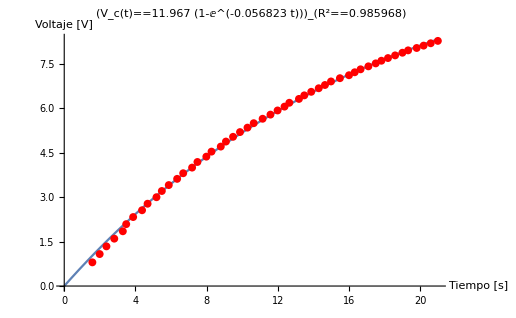

```mathematica
graficocar12=Show[Plot[voltcarga12,{t,0,Last[tc12]}],ListPlot[carga12,PlotStyle->Red],AxesLabel->{Style["Tiempo [s]",Black,13],Style["Voltaje [V]",Black,13]},PlotLabel->Style[Underscript["V_c(t)"== voltcarga12, R^2 == Correlation[tc12,vc12]],Black,15]]
```

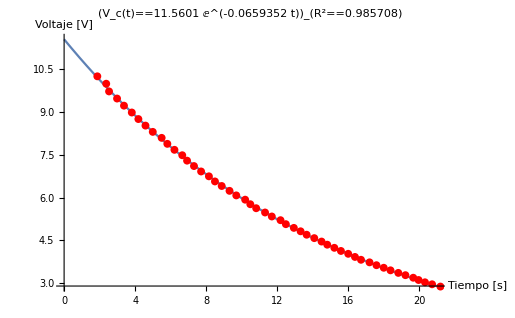

```mathematica
Show[Plot[voltajedescar12,{t,0,Last[tc12]}],ListPlot[descarga12,PlotStyle->Red],AxesLabel->{Style["Tiempo [s]",Black,13],Style["Voltaje [V]",Black,13]},PlotLabel->Style[Underscript["V_c(t)" == voltajedescar12, R^2 == Abs[Correlation[td12,vd12]]],Black,15]]
```

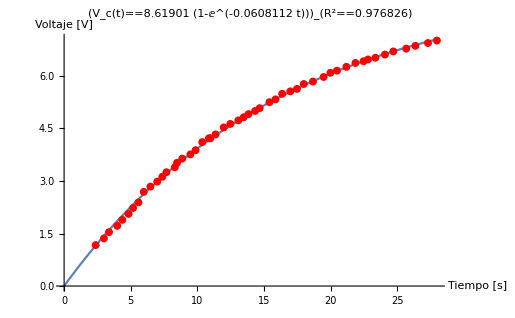

```mathematica
Show[Plot[voltajecarga9,{t,0,Last[tc9]}],ListPlot[carga9,PlotStyle->Red],AxesLabel->{Style["Tiempo [s]",Black,13],Style["Voltaje [V]",Black,13]},PlotLabel->Style[Underscript["V_c(t)"== voltajecarga9, R^2 == Correlation[tc9,vc9]],Black,15]]
```

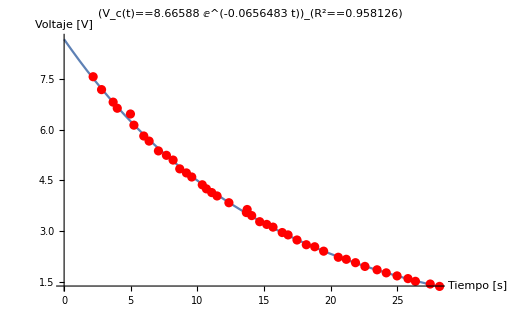

```mathematica
Show[Plot[voltajedescar9,{t,0,Last[tc9]}],ListPlot[descarga9,PlotStyle->Red],AxesLabel->{Style["Tiempo [s]",Black,13],Style["Voltaje [V]",Black,13]},PlotLabel->Style[Underscript["V_c(t)" == voltajedescar9, R^2 == Abs[Correlation[td9,vd9]]],Black,15]]
```

```mathematica
listaTau=τ/.{conc12,cond12,conc9,cond9}
```

{17.598510208276963, 15.166410839622753, 16.444327713215905, 15.232689156005804}

```mathematica
expτ=Mean[listaTau]
```

16.1105

```mathematica
τreal
```

13.622

```mathematica
errorTau=100*(τreal-listaTau)/τreal
```

{-29.1918,-11.3376,-20.7189,-11.8242}

```mathematica
Mean[errorTau]
```

-18.2681

```mathematica
errorTauS=100*(expτ-τreal)/expτ
```

15.4464

```mathematica
(*errores en mediciones*)
eitau=Sqrt[(22*0.05)^2+(69.5*0.05)^2]
```

3.64495